Add ‘ng’ to H,Ψ:

```mathematica
ng0=0.1;n0=0;EC0=0.214;EJ0=52;
```

Cottet’s Thesis formulation - only valid  0<n_g<0.5

```mathematica
EmCottet[x0_,k0_]:=Module[{ng=x0,k=k0},EC=EC0;EJ=EJ0;
r=k+1-Mod[k+1,2]+2ng(-1)^k;
q=-EJ/(2EC);
EC MathieuCharacteristicA[r,q]]
```

```mathematica
FmCottet[x0_,k0_,z0_]:=Module[{ng=x0,k=k0,z=z0},EC=EC0;EJ=EJ0;
r=k+1-Mod[k+1,2]+2ng(-1)^k;
q=-EJ/(2EC);
Exp[I ng z]/(√(2π))(MathieuC[MathieuCharacteristicA[r,q],q,z/2]+I(-1)^(k+1) MathieuS[MathieuCharacteristicA[r,q],q,z/2])]
```

```mathematica
Em[x0_,k0_]:=Module[{ng=x0,k=k0},EC=EC0;EJ=EJ0;
Sort[Table[Module[{},r=kk+1-Mod[kk+1,2]+2ng(-1)^kk;
q=-EJ/(2EC);
EC MathieuCharacteristicA[r,q]],{kk,0,6}]][[k+1]]]
```

```mathematica
Em2[x0_]:=Module[{ng=x0},EC=EC0;EJ=EJ0;
Sort[Table[Module[{},r=kk+1-Mod[kk+1,2]+2ng(-1)^kk;
q=-EJ/(2EC);
EC MathieuCharacteristicA[r,q]/EJ0],{kk,0,40}]]]
```

```mathematica
Em2[0.0000001]
```

{-0.910317,-0.733085,-0.560203,-0.391851,-0.228237,-0.0696045,0.0837589,0.231503,0.373188,0.508254,0.635831,0.755432,0.860329,0.970515,1.01376,1.1827,1.18569,1.43233,1.43239,1.72474,1.72474,2.05607,2.05607,2.42406,2.42406,2.82747,2.82747,3.26555,3.26555,3.73783,3.73783,4.24398,4.24398,4.78377,4.78377,5.35706,5.35706,5.96371,5.96371,6.60365,6.60365}

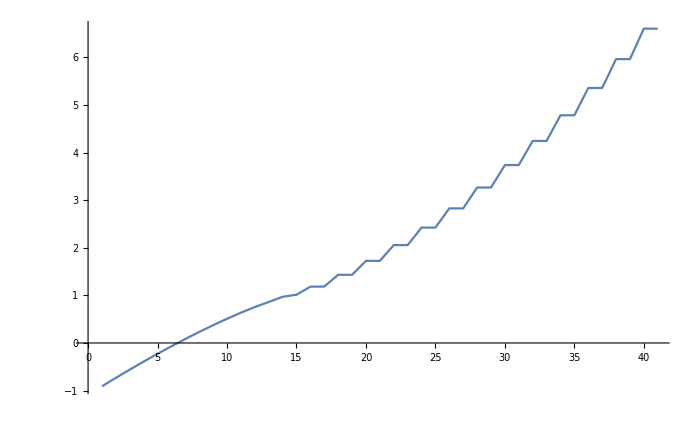

```mathematica
ListLinePlot[%]
```

```mathematica
Em[0.1,2]
```

1.16276

```mathematica
Fm[x0_,k0_,z0_]:=Module[{ng=x0,k=k0,z=z0},EC=EC0;EJ=EJ0;
rec=Sort[Table[{Module[{},r=kk+1-Mod[kk+1,2]+2ng(-1)^kk;
q=-EJ/(2EC);
MathieuCharacteristicA[r,q]],kk},{kk,0,6}]][[k+1]];
Exp[I ng z]/(√(2π))(MathieuC[rec[[1]],q,z/2]+I(-1)^(rec[[2]]+1) MathieuS[rec[[1]],q,z/2])]
```

```mathematica
t=Table[EmCottet[0.1,k],{k,0,5}]
```

{-7.62805,-3.0512,1.16336,4.98584,7.95442,11.4757}

```mathematica
t=Table[Em[0.1,k],{k,0,5}]
```

{-7.62805,-3.0512,1.16336,4.98584,7.95442,11.4757}

```mathematica
√(8EJ0 EC0)-EC0
```

4.59898

```mathematica
t[[2]]-t[[1]]
```

4.57685

```mathematica
t[[3]]-2t[[2]]+t[[1]]
```

-0.362288

Mathieu exponential function (em_ν(z,q))

```mathematica
Zm[x0_,k0_,z0_]:=Module[{ng=x0,k=k0,z=z0},EC=EC0;EJ=EJ0;
rec=Sort[Table[{Module[{},r=kk+1-Mod[kk+1,2]+2ng(-1)^kk;
q=-EJ/(2EC);
MathieuCharacteristicA[r,q]],kk,r},{kk,0,6}]][[k+1]];Print[rec];
(MathieuC[rec[[1]],q,z]+I MathieuS[rec[[1]],q,z])]
```

test quasi-periodicity (Floquet) of Mathieu’s functions

```mathematica
Zm[ng0,0,1.1+π]
```

{-25.4268,0,0.2}

0.0245247+0.0178411 ⅈ

```mathematica
Exp[I π (.2)]Zm[ng0,0,1.1]
```

{-25.4268,0,0.2}

0.0245247+0.0178411 ⅈ

test 2π-periodicity (note: it depends on the sign of 2ng!!!)

```mathematica
Exp[-I ng0 (1.1)]/(√(2π))Zm[ng0,0,1.1/2]
Exp[-I ng0 (1.1+2π)]/(√(2π))Zm[ng0,0,(1.1+2π)/2]
```

{-25.4268,0,0.2}

0.275083-0.0303811 ⅈ

{-25.4268,0,0.2}

0.275083-0.0303811 ⅈ

some basic tests: periodicity and the connection between ng and ng+0.5

```mathematica
Fm[0.05,1,-.2]
Fm[0.05,1,-.2+2π]
```

-0.00326038-0.326915 ⅈ

-0.00326038-0.326915 ⅈ

```mathematica
Fm[0.75,1,-0.3]
Exp[-I 0.3]Conjugate[Fm[0.25,1,-0.3]]
```

0.104289+0.455551 ⅈ

0.104289+0.455551 ⅈ

```mathematica
NIntegrate[Conjugate[Fm[0.25,0,z]]D[Fm[0.25,1,z],z],{z,0,2π}]
```

-2.05086×10^-10+0.976079 ⅈ

```mathematica
NIntegrate[(1+Exp[-I z])Conjugate[Fm[0.13,0,z]]Fm[0.13+0.5,1,z],{z,0,2π}]
```

0.0000166936+1.83223×10^-12 ⅈ

```mathematica
Fm[0.499,1,z]
Simplify[Exp[I z]Conjugate[Fm[1-0.499,1,z]],Assumptions->{z∈Reals}]
```

1/(√(2 π))ⅇ^((0.+0.499 ⅈ) z) (MathieuC[-10.1715,-16.6667,z/2]+ⅈ MathieuS[-10.1715,-16.6667,z/2])

1/(√(2 π))ⅇ^((0.+0.499 ⅈ) z) (Conjugate[MathieuC[-10.1715,-16.6667,z/2]]+ⅈ Conjugate[MathieuS[-10.1715,-16.6667,z/2]])

```mathematica
Fm[0.499,1,z]
Fm[0.501,1,z]
```

1/(√(2 π))ⅇ^((0.+0.499 ⅈ) z) (MathieuC[-10.1715,-16.6667,z/2]+ⅈ MathieuS[-10.1715,-16.6667,z/2])

1/(√(2 π))ⅇ^((0.+0.501 ⅈ) z) (MathieuC[-10.1715,-16.6667,z/2]-ⅈ MathieuS[-10.1715,-16.6667,z/2])

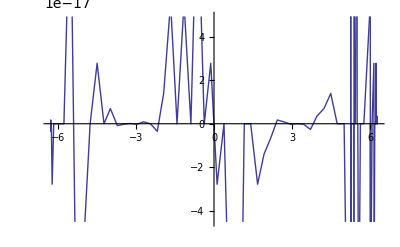

```mathematica
Plot[{Im[Fm[0.499,1,z]]-Im[Exp[I z]Conjugate[Fm[1-0.499,1,z]]]},{z,-2π,2π}]
```

testing size of dipole matrix elements (for interband dipole estimate)

```mathematica
F=MathieuC[-25.426847625207596,-16.666666666666668,z/2]-ⅈ MathieuS[-25.426847625207596,-16.666666666666668,z/2];
FC=MathieuC[-25.426847625207596,-16.666666666666668,z/2]+ⅈ MathieuS[-25.426847625207596,-16.666666666666668,z/2];
NIntegrate[I FC D[F,z],{z,0,2π}]
NIntegrate[I F D[FC,z],{z,0,2π}]
```

0.0000233406-2.01642×10^-15 ⅈ

-0.0000233406-2.01642×10^-15 ⅈ

testing size of Majorana Hamiltonian matrix elements

```mathematica
NIntegrate[(1+Exp[-I z])Conjugate[Fm[0.2,0,z]]Fm[0.2+0.5,1,z],{z,0,2π}]
NIntegrate[(1+Exp[I z])Conjugate[Fm[0.2+0.5,0,z]]Fm[0.2,1,z],{z,0,2π}]
```

0.0000217799-1.31617×10^-13 ⅈ

0.0000217814-9.47908×10^-13 ⅈ

```mathematica
(1+Exp[-I z])Conjugate[Fm[0.2,0,z]]Fm[0.2+0.5,0,z]
```

1/(2 π)ⅇ^((0.+0.7 ⅈ) z-(0.+0.2 ⅈ) Conjugate[z]) (1+ⅇ^(-ⅈ z)) (Conjugate[MathieuC[-25.4268,-16.6667,z/2]]+ⅈ Conjugate[MathieuS[-25.4268,-16.6667,z/2]]) (MathieuC[-25.4268,-16.6667,z/2]+ⅈ MathieuS[-25.4268,-16.6667,z/2])

```mathematica
c=MathieuC[-25.426843601800325,-16.666666666666668,z/2];s=MathieuS[-25.426843601800325,-16.666666666666668,z/2];
cp=MathieuC[-25.426838628582214,-16.666666666666668,z/2];sp=MathieuS[-25.426838628582214,-16.666666666666668,z/2];
NIntegrate[2/(2π)Cos[z/2]*(c*sp+cp*s),{z,0,2π}]
```

6.58554×10^-10

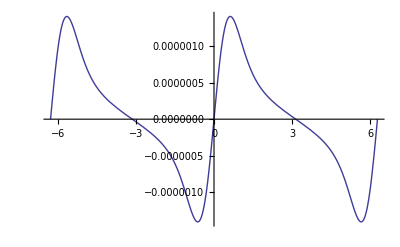

```mathematica
Plot[2/(2π)Cos[z/2]*(c*sp+cp*s),{z,-2π,2π}]
```

```mathematica
TrigExpand[Simplify[ⅇ^((0.+0.75 ⅈ) z-(0.+0.25 ⅈ) Conjugate[z]) (1+ⅇ^(-ⅈ z)),Assumptions->{z∈Reals,z<∞}]]
```

ⅇ^((0.-0.5 ⅈ) z)+ⅇ^((0.+0.5 ⅈ) z)

```mathematica
Simplify[(1+Exp[-I z])Conjugate[Fm[0.25,0,z]]Fm[0.25+0.5,0,z],Assumptions->{z∈Reals}]
```

1/(2 π)ⅇ^((0.-0.5 ⅈ) z) (1+ⅇ^(ⅈ z)) (Conjugate[MathieuC[-25.4268,-16.6667,z/2]]+ⅈ Conjugate[MathieuS[-25.4268,-16.6667,z/2]]) (MathieuC[-25.4268,-16.6667,z/2]+ⅈ MathieuS[-25.4268,-16.6667,z/2])

Verifying eigenstate+eigenvalue with ng included in H

```mathematica
ng0=0.622;n0=0;
```

```mathematica
W=Fm[ng0,n0,z];DFm=Simplify[4EC( -D[D[W,z],z]-2 ng0/I D[W,z]+ng0^2 W)-EJ Cos[z]W]
```

ⅇ^((0.+0.622 ⅈ) z) (-3.04315 MathieuC[-25.4268,-16.6667,0.5 z]+(0.+3.91485×10^-17 ⅈ) MathieuCPrime[-25.4268,-16.6667,0.5 z]-(0.+3.04315 ⅈ) MathieuS[-25.4268,-16.6667,0.5 z]-3.91485×10^-17 MathieuSPrime[-25.4268,-16.6667,0.5 z])

```mathematica
W2=Em[ng0,n0]*W
```

-3.04315 ⅇ^((0.+0.622 ⅈ) z) (MathieuC[-25.4268,-16.6667,z/2]+ⅈ MathieuS[-25.4268,-16.6667,z/2])

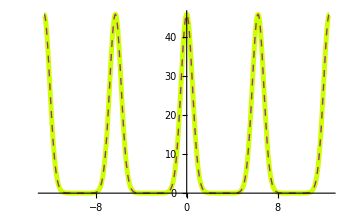

```mathematica
Plot[{Abs[DFm]^2,Abs[W2]^2},{z,-4π,4π},PlotRange->All,PlotStyle->{{Hue[0.2],Thickness[0.01]},Dashed}]
```

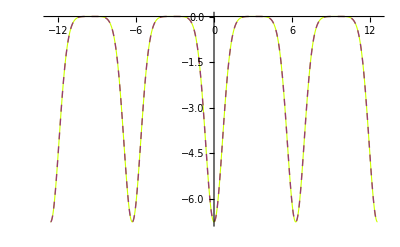
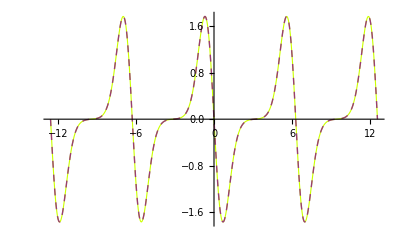

```mathematica
{{Plot[{Re[DFm],Re[W2]},{z,-4π,4π},PlotRange->All,PlotStyle->{{Hue[0.2],Thickness[0.002]},Dashed}]}, {Plot[{Im[DFm],Im[W2]},{z,-4π,4π},PlotRange->All,PlotStyle->{{Hue[0.2],Thickness[0.002]},Dashed}]}}
```

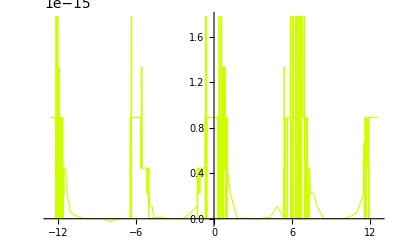

```mathematica
Plot[{Re[DFm-W2]},{z,-4π,4π},PlotRange->All,PlotStyle->{{Hue[0.2],Thickness[0.002]},Dashed}]
```